## Twitter

```mathematica
tw = ServiceConnect["Twitter"]
```

ServiceObject[…]

### Usuario

```mathematica
twlist=tw["TweetList", "Username"->"AristeguiOnline","Elements"-> "FullData",MaxItems->200]
TableForm@Normal@Keys@First@twlist
```

ID
Text
Date
Hashtags
Location
Username
Name
ProfileImageThumbnail
RetweetCount
FavoriteCount
URL

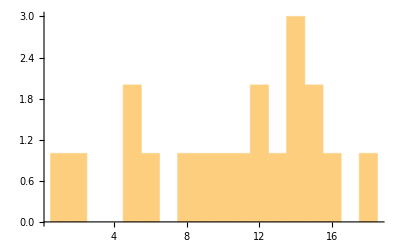

```mathematica
Histogram[CountsBy[twlist[[All,"Date"]],#["Hour"]&],24]
```

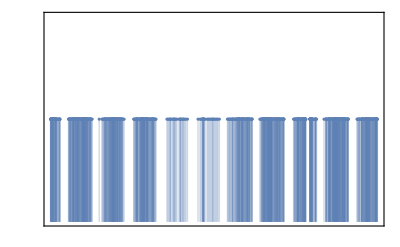

```mathematica
ttl=tw["TweetTimeline", "Username"->"Forbes_Mexico",MaxItems->1000]
```

### Hyperlink

```mathematica
wihyperlinks=Select[TextWords@#["Text"],StringMatchQ["http"~~__]]&/@Normal@twlist[[1;;5]]
```

{{https://t.co/9u2OjNpX02,https://t.co/lDbnO7UjRA},{https://t.co/bCsr3R3WZR,https://t.co/J7Rgv0Hftw},{https://t.co/GESgyS84jl,https://t.co/0AieIAXuJx},{https://t.co/emLYlrMjjd,https://t.co/lm6ZLfKPBJ},{https://t.co/doBnfEo9ER,https://t.co/Jwo2PWsPF9}}

### Cuentas HUBs

```mathematica
HUBs=tw["UserIDSearch","Query"->"#Coronavirus",MaxItems->20];
Dataset[tw["UserData","UserID"->#]&/@HUBs]
```

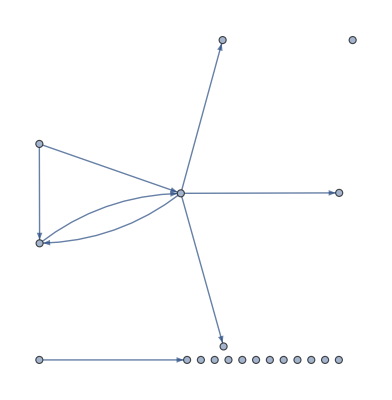

```mathematica
tw["SearchMentionNetwork","Query"->"#Coronavirus"]
```

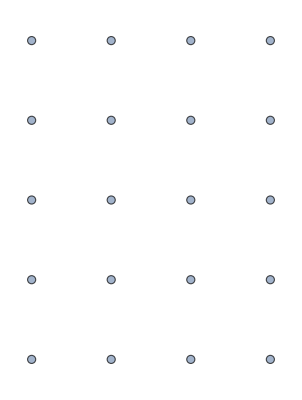

```mathematica
tw["SearchReplyToNetwork","Query"->"#Coronavirus"]
```

### Tweets HUBs

```mathematica
searchHUBs=tw["TweetSearch","Query"->"#Coronavirus",MaxItems->500,Language->Entity["Language","Spanish"],"ResultType"-> "Popular"]
```

```mathematica
keys = Keys@First@searchHUBs
```

### Localidad

```mathematica
loc=FindGeoLocation[Entity["City", {"Saltillo","Coahuila","Mexico"}]];
GeoGraphics@GeoDisk[loc,Quantity[30,"km"]]
```

-Graphics-

```mathematica
searchloc=tw["TweetSearch","Query"->"#Coronavirus",MaxItems->20,GeoLocation->loc,"Radius"-> Quantity[30, "Kilometers"]]
```

```mathematica
Keys@First@searchloc
```

### Frecuencias

```mathematica
FilterTweets[tweets_]:=StringReplace[RemoveDiacritics@ToLowerCase@tweets,{RegularExpression["[http]*[s]*[:][\\/\\/][a-z0-9.\\/]+[ ]*"]->" ",RegularExpression["[rt: ]*[rt ]*[\\@][a-z0-9]*[:]*"]->" ",RegularExpression["[^a-z\\s:]"]|":"->" "}];
```

```mathematica
tweets=FilterTweets[#["Text"]]&/@(Normal@searchHUBs);
```

```mathematica
Stopwords=Import["https://countwordsfree.com/stopwords/spanish","Data"][[2,All,2]];
```

```mathematica
RemoveStopWords[doc_,stopWords_]:=StringDelete[doc,WordBoundary~~Alternatives@@stopWords~~WordBoundary,IgnoreCase->True];
```

```mathematica
processedTweets=Select[DeleteDuplicates[RemoveStopWords[TextWords[#],Stopwords]],Not@*StringMatchQ[""]]&/@tweets;
```

```mathematica
significantWords=Take[Reverse[SortBy[Tally[Flatten[processedTweets]],Last]],10];
quantities=N[#[[2]]/Length@tweets]&/@significantWords;
pieChart=PieChart[quantities,ChartLabels->Placed[significantWords⟦All,1⟧,"RadialCallout"],LabelingFunction->(PercentForm@*N@#&)]
```

-Graphics-